# Assignment 2

Course code: IX1500
Date: 20yy-mm-dd

Leo Karsikas, leoka@kth.se
Jonathan Johnson, jjohnso@kth.se

Task 1: RSA

## Summery

### Task

Ni ska använda RSA kryptering för att kryptera ovanstående citat (se 2.2.4 ovan), där n skall vara högst 200 bitar och e ett litet tal, ca 10^3-10^4 stort. Se 2.2.4 för hur dessa ska generas. Koda citatet enligt metoden i 2.2.4 (tal med basen 256). Observera att om meddelandet kodas till talet m så måste m < n. Om inte, så dela upp citatet på flera rader och kryptera varje rad för sig. Tips: Funktioner som kan behövas: FactorInteger, Partition.

Dekryptera sedan meddelandet och verifirera att ni får samma resultat som ursprunget.

Undersök sedan sambandet mellan nyckellängd (i bitar) och tid för att kryptera och dekryptera meddelanden. Rita en graf för sambandet mellan nyckelängd, n , och exekveringstid. Låt n variera upp till 2048 bitar. Tips: Funktion: Timing

### Solution

1. The first step in the solution is to decide p and q as two large prime number between 2^99 and 2^100 to built n=p*q . 
2. Next step is to choose the encryption key e which is relative prime to 
ϕ=(p-1)(q-1) . The e key with n makes up the public key (n,e) . 
Where re creating a while loop that test random integers in between the given domain n until it finds which is not a relative prime. 
3. To encrypt the message we need to  the private key d. Finding an inverse to d to e in the ℤ_ϕ where d e=1 mod(ϕ) where d is used for decryption key. 
4. The decryption algorithm we need the as said above the private key d and n. 

The encryption  and decryption algorithm:
Encryption algorithm: 
C≡M^e mod n
Where C is the encrypted message, M is the message and e and n that makes up the public key. 

Decryption algorithm: 
D≡ C^d mod n  
Where D is the decrypted message and d is the private key. 

The reason why is works: 
D=C^d=(M^e)^d=M^ed 

Because e and d  is inverses in ℤ_(ϕ(n))

Therefore ed=1+k(ϕ(n)), and that means 
M^ed=M^(1+k(ϕ(n)))=M*(M^(ϕ(n)))^k

Using the Euleres Tuotient Theorem:
M^(ϕ(n))≡ 1 mod n 
Can we see that: D≡ M mod n

### Result

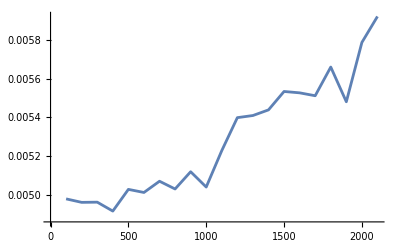
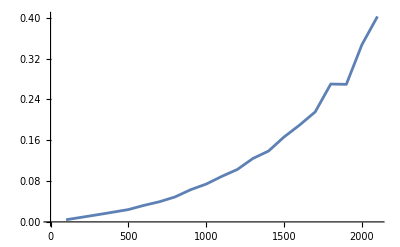
As predicted, with the relatively small chosen value for e, encryption is far faster than decryption. We can also see that the encryption and decryption speeds as a function of key length ∈Ο(n^2)

Decryption:
-Graphics-

Encryption:
-Graphics-

## Task 1

### Model for ...

...

### Model for ...

...

## Code

```mathematica
ClearAll["`*"]
```

First we generate our keys; p,q,n,d,e.
we put this inside a function, this makes it easier later when we are benchmarking

```mathematica
generateKeys[bits_] :=
Module[{},
p = RandomPrime[{2^(bits/2 -1),2^(bits/2)}];
q=RandomPrime[{2^(bits/2 -1),2^(bits/2)}];
n = p q;
ϕ = (p-1) (q-1);
rndInt := RandomInteger[{10^3,10^4}];
While[GCD[e=rndInt, ϕ]≠1];
d =PowerMod[e,-1,ϕ];
]
```

We put the encryption/decryption specific PowerMod calls into functions so we can easily map them over lists later.
We do the same with the encode/decode functions.

```mathematica
encrypt[x_] := PowerMod[x,e,n]
decrypt[x_] := PowerMod[x,d,n]

B=256;
encode[x_] := x. B^(Range[Length[x]]-1)
decode[0] := {}
decode[x_]:= Flatten[{Mod[x,B],decode[Quotient[x,B]]}]
```

These functions puts it all in a neat package, encodeEncrypt takes a string and outputs a cipher, decodeDecrypt takes a cipher and outputs a string.

```mathematica
encodeEncrypt[message_] :=
Module[{m,B},m=message;
m = Partition[ToCharacterCode[m],UpTo[20]];
m = Map[encode,m];
m=Map[encrypt,m]]

decodeDecrypt[crypt_] :=
Module[{d,B},d=crypt;
d = Map[decrypt,d];
d = Flatten[Map[decode, d]];
d = FromCharacterCode[d]]
```

```mathematica
generateKeys[200];
```

```mathematica
message = "A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them.Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark.
asdfasdf";
```

```mathematica
crypt = encodeEncrypt[message];
decrypted = decodeDecrypt[crypt]
```

```mathematica
generateKeys[4096];
time[bits_]:=
Module[{s},s={1,2};
generateKeys[bits];
s[[1]] ={bits, Timing[crypt = encodeEncrypt[message];][[1]]};s[[2]]={bits, Timing[messageout =  decodeDecrypt[crypt];][[1]]};
s]
times =Map[time,Range[100,2100,100]];

ListPlot[{times[[All,1]]},{Joined -> True}]
ListPlot[{times[[All,2]]},{Joined -> True}]
```

-Graphics-

-Graphics-

crack:

```mathematica
generateKeys[100];
cipher = encodeEncrypt[message];
RSAcrack[cipher_,n_,e_] :=
Module[{y},y=0;
y= FactorInteger[n]
]
FactorInteger[n]
```

$Aborted